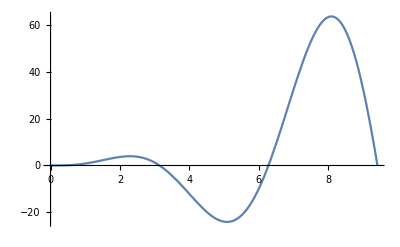

```mathematica
Plot[Evaluate[Input["Please input a function of x to plot on the interval"]],{x,0,3 π}]
```

#### Linear Programming Problem

minimize          1000 x_1+1200 x_2
subject to       10 x_1+5 x_2≤200
					2 x_1+3 x_2≤60
					x_1≤34
					x_2≤14
					x_1,x_2≥0

```mathematica
LinearProgramming[{-1000,-1200},{{-10,-5},{-2,-3}},{-200,-60},{-34,-14}]
```

{15,10}

```mathematica
LinearProgramming[{-1000,-1200},{{10,5},{2,3}},{{200,-1},{60,-1}},{{-Infinity,34},{-Infinity,14}}]
```

{15,10}

```mathematica
Maximize[{1000x + 1200y, {10x + 5y ≤200&&2x + 3y≤60&&x≤34&&y≤14}},{x,y}]
```

{27000,{x→15,y→10}}

```mathematica
FindMaximum[{1000x + 1200y, {10x + 5y ≤200&&2x + 3y≤60&&x≤34&&y≤14}},{x,y}]
```

{27000.,{x→15.,y→10.}}

#### Quadratic Programming Problem

minimize           f_o[x]=1/2 x_1^2+x_2^2-x_1 x_2-2 x_1-6 x_2
subject to        x_1+x_2\[VectorLessEqual]2
					-x_1+2 x_2\[VectorLessEqual]2
					2 x_1+x_3\[VectorLessEqual]3

```mathematica
{q,c}={{{1,-1},{-1,2}},{-2,-6}};
{a,b}={-{{1,1},{-1,2},{2,1}},{2,2,3}};
QuadraticOptimization[{q,c},{a,b}]
```

{0.666667,1.33333}

```mathematica
1/2*{2/3,4/3}.{{1,-1},{-1,2}}.{2/3,4/3}//N
```

1.11111

#### A Quadratic function is represented visually as an ellipsoid

Such functions can be re-written in the standard form of an ellipsoid

```mathematica
ContourPlot3D[{0.5,0.5,1}.{x^2,y^2,z^2}+{1,1,1}.{x,y,z}-10==1,{x,-10.5,10.5},{y,-10.5,10.5},{z,-10.5,10.5},PlotRange->Full]
```

-Graphics3D-

#### Relationship between Single Value Decomposition and EigenValues

```mathematica
Eigenvalues[{{1,-1},{-1,2}}]//N
```

{2.61803,0.381966}

```mathematica
SingularValueDecomposition[{{1,-1},{-1,2}}]//N
```

{{{-0.525731,0.850651},{0.850651,0.525731}},{{2.61803,0.},{0.,0.381966}},{{-0.525731,0.850651},{0.850651,0.525731}}}

#### Linear Optimization Problem

minimize          2 x_1+x_2
subject to       -x_1+x_2≤1
					x_1+x_2≥2
					x_2≥0
					x_1-2 x_2≤4

```mathematica
c = {2, 1};
{a, b} = {({{1, -1}, {1, 1}, {0, 1}, {-1, 2}}),{1,-2,0,4}};
```

```mathematica
LinearOptimization[c,{a,b}]
```

{1/2,3/2}

#### Linear Fractional Optimization Problem

```mathematica
LinearFractionalOptimization
```

#### Quadratic Optimization Problem

minimize          2 x_1^2+x_2^2+x_1 x_2+x_1+x_2
subject to       x_1≥0
					x_2≥0
					x_1+x_2=1

Re-writing the problem in the standard from of a quadratic Program Problem, where X={x_1,x_2}

minimize          1/2 X^T(4 | 1
1 | 2)X + (1 | 1)X
subject to       (1 | 0
0 | 1)X≥(0
0)
					(1 | 1)x=1

```mathematica
Clear[q,c,a,b]
```

```mathematica
{q,c}={({{4, 1}, {1, 2}}),{1,1}};
{a,b}={({{1, 0}, {0, 1}}),{0,0}};
{aeq,beq}={{{1,1}},{-1}};
```

```mathematica
QuadraticOptimization[{q,c},{a,b},{aeq,beq}]
```

{0.25,0.75}

#### Second Order Cone Optimization

minimize          -2 x_1+x_2+5 x_3
subject to       ‖(-13 x_1+3 x_2+5 x_3-3
-12 x_1+12 x_2-6 x_3-2)‖≤-12 x_1-6 x_2+5 x_3-12
					‖(-3 x_1+6 x_2+2 x_3
x_1+9 x_2+2 x_3+3
-x_1-19 x_2+3 x_3-42)‖≤-3 x_1+6 x_2-10 x_3+27

```mathematica
Clear[c,a1,b1,α1,β1,a2,b2,α2,β2]
```

```mathematica
c={-2,1,5};
{a1,b1}={({{-13, 3, 5}, {-12, 12, -6}}),{-3,-2}};
{α1,β1}={{-12,-6,5},-12};
{a2,b2}={({{-3, 6, 2}, {1, 9, 2}, {-1, -19, 3}}),{0,3,-42}};
{α2,β2}={{-3,6,-10},27};
```

```mathematica
SecondOrderConeOptimization[c,{{a1,b1,α1,β1},{a2,b2,α2,β2}}]
```

{-5.01479,-5.76693,-8.5218}

#### Semi Definite Optimization

minimize          x_1-x_2+x_3
subject to       x_1≥0
					x_2≥0
					x_1+x_2=1

```mathematica
Clear[Subscript[a, 0],Subscript[a, 1],Subscript[a, 2]]
```

```mathematica
c={1,-1,1};
Subscript[a, 0]=({{33, -9}, {-9, 26}});Subscript[a, 1]=-({{-7, -11}, {-11, 3}}); Subscript[a, 2]=-({{7, -18}, {-18, 8}}); Subscript[a, 3]=-({{-2, -8}, {-8, 1}});
Subscript[b, 0]=({{14, 9, 40}, {9, 91, 10}, {40, 10, 15}}); Subscript[b, 1]=-({{-21, -11, 0}, {-11, 10, 8}, {0, 8, 5}}); Subscript[b, 2]=-({{0, 10, 16}, {10, -10, -10}, {16, -10, 3}});  Subscript[b, 3]=-({{-5, 2, -17}, {2, -6, 8}, {-17, 8, 6}});
```

```mathematica
SemidefiniteOptimization[c,{{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]},{Subscript[b, 0],Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]}}]
```

StringForm::sfq: Unmatched backquote in The length, `1` of the list of matrices at position `2` is not the same as the length, `3`, of the vector at position `4..

SemidefiniteOptimization::vmlen: The length, `1` of the list of matrices at position `2` is not the same as the length, `3`, of the vector at position `4.

SemidefiniteOptimization[{1,-1,1},{{{{33,-9},{-9,26}},{{7,11},{11,-3}},{{-7,18},{18,-8}},{{2,8},{8,-1}}},{{{14,9,40},{9,91,10},{40,10,15}},{{21,11,0},{11,-10,-8},{0,-8,-5}},{{0,-10,-16},{-10,10,10},{-16,10,-3}},{{5,-2,17},{-2,6,-8},{17,-8,-6}}}}]

```mathematica
ConicOptimization
```